```mathematica
f[x_,a_]:=-((a^2)+(x^2))^(-1/2)
```

```mathematica
g[x_,a_]:=-x*(((a^2)+(x^2))^(-3/2))
```

```mathematica
h[x_,a_]:=-x/((a^3)+((3/2)*a*(x^2)))
```

```mathematica
Manipulate[Plot[g[x,a],{x,-20,20},PlotRange->All],{a,0,10}]
```

```mathematica
,
```

```mathematica
Series[f[x],{x,0,4}]
```

8+3 x^2+(3 x^4)/16+O[x]^5

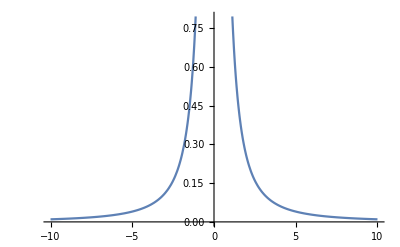

```mathematica
Plot[1/(x^2),{x,-10,10}]
```

```mathematica
F[x_]:=-C*Q*q*x/(((d^2)+(x^2))^(3/2))
```

```mathematica
F'[x]
```

(3 C q Q x^2)/((d^2+x^2)^(5/2))-(C q Q)/((d^2+x^2)^(3/2))

```mathematica
Solve[(3 C q Q x^2)/((d^2+x^2)^(5/2))-(C q Q)/((d^2+x^2)^(3/2))==0,x]
```

{{x→-d/(√2)},{x→d/(√2)}}

```mathematica
Simplify[-3 C q Q x^2 √(d^2+x^2)-C q Q (d^2+x^2)^(3/2)]
```

-C q Q √(d^2+x^2) (d^2+4 x^2)

```mathematica
Solve[-C q Q √(d^2+x^2) (d^2+4 x^2)==0,x]
```

{{x→-(ⅈ d)/2},{x→(ⅈ d)/2},{x→-ⅈ d},{x→ⅈ d}}

```mathematica
Simplify[-3 C q Q x^2 √(d^2+x^2)-C q Q (d^2+x^2)^(3/2)]
```

-C q Q √(d^2+x^2) (d^2+4 x^2)

```mathematica
Solve[-c q Q √(d^2+x^2) (d^2+4 x^2)==0,x]
```

{{x→-(ⅈ d)/2},{x→(ⅈ d)/2},{x→-ⅈ d},{x→ⅈ d}}

```mathematica
Solve[{0==-3 C q Q x^2 √(d^2+x^2)-C q Q (d^2+x^2)^(3/2),x<0},x]
```

{{x→ConditionalExpression[-√(Im[d]^2),Re[d]==0]},{x→ConditionalExpression[-1/2 √(Im[d]^2),Re[d]==0]}}

```mathematica
C
```

C

```mathematica
Q
```

Q

```mathematica
q
```

q

```mathematica
d
```

d

```mathematica
G[x_]:=-x*(((a^2)+(x^2))^(-3/2))
```

```mathematica
G'[x]
```

```mathematica
Solve[G'[x]==0,x]
```

{{x→-a/(√2)},{x→a/(√2)}}

```mathematica
c= 9*10^9;Q=1.6*10^-19;q= -1.6*10^-19;d=-2*10^-10;m=9.11*10^-31
```

9.11×10^-31

```mathematica
Sqrt[c*q*Q/(m*(d^3))]
```

5.6226×10^15

```mathematica
U[x_]:=((x^4)-((l^2)*(x^2)))*(U0/(l^4))
```

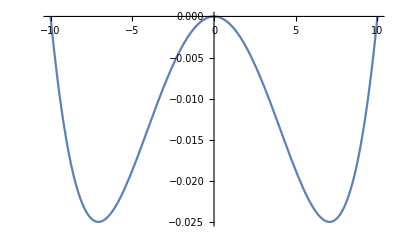

```mathematica
Plot[U[x,10,0.1],{x,-10,10}]
```

```mathematica
U'[x]
```

(U0 (-2 l^2 x+4 x^3))/l^4

```mathematica
Roots[(U0 (-2 l^2 x+4 x^3))/l^4==0,x]
```

x==0||x==l/(√2)||x==-l/(√2)

```mathematica
(x0+x)^3
```

(x+x0)^3

```mathematica
Expand[(x+x0)^3]
```

x^3+3 x^2 x0+3 x x0^2+x0^3

```mathematica
F[x_]:=(2U0 ( l^2 x-2 x^3))/l^4
```

```mathematica
x0=l/Sqrt[2]
```

l/(√2)

```mathematica
U[x0]+U'[x0]*(x-x0)+(1/2)*U''[x0]*(x-x0)^2+(1/6)*U'''[x0]*(x-x0)^3
```

-U0/4+(2 U0 (-l/(√2)+x)^2)/l^2+(2 √2 U0 (-l/(√2)+x)^3)/l^3

```mathematica
U[x0]+U'[x0]*(x-x0)+(1/2)*U''[x0]*(x-x0)^2
```

-U0/4+(2 U0 (-l/(√2)+x)^2)/l^2

```mathematica
Simplify[-U0/4+(2 U0 (-l/(√2)+x)^2)/l^2]
```

U0 (3/4-(2 √2 x)/l+(2 x^2)/l^2)

```mathematica
Simplify[-U0/4+(2 U0 (-l/(√2)+x)^2)/l^2+(2 √2 U0 (-l/(√2)+x)^3)/l^3]
```

-(U0 (l^3-4 √2 l^2 x+16 l x^2-8 √2 x^3))/(4 l^3)

```mathematica
F'[x0]*(x-x0)+(1/2)*F''[x0]*(x-x0)^2
```

-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3

```mathematica
Expand[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3]
```

```mathematica
(-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3)/(2*U0/l^2)
```

(l^2 (-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3))/(2 U0)

```mathematica
Simplify[(l^2 (-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3))/(2 U0)]
```

-l/(√2)+4 x-(3 √2 x^2)/l

```mathematica
Factor[-l/(√2)+4 x-(3 √2 x^2)/l]
```

-(√2 l^2-8 l x+6 √2 x^2)/(2 l)

```mathematica
Simplify[-(√2 l^2-8 l x+6 √2 x^2)/(2 l)]
```

-l/(√2)+4 x-(3 √2 x^2)/l

```mathematica
Factor[-l/(√2)+4 x-(3 √2 x^2)/l]
```

-(√2 l^2-8 l x+6 √2 x^2)/(2 l)

```mathematica
Expand[-(√2 l^2-8 l x+6 √2 x^2)/(2 l)]
```

-l/(√2)+4 x-(3 √2 x^2)/l

```mathematica
FullSimplify[-l/(√2)+4 x-(3 √2 x^2)/l]
```

4 x-(l^2+6 x^2)/(√2 l)

```mathematica
Simplify[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3]
```

-(U0 (√2 l-2 x) (l-3 √2 x))/l^3

```mathematica
Expand[-(U0 (√2 l-2 x) (l-3 √2 x))/l^3]
```

-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3

```mathematica
Simplify[-(12 U0 (x-x0)^2 x0)/l^4+(2 U0 (x-x0) (l^2-6 x0^2))/l^4+(2 U0 (l^2 x0-2 x0^3))/l^4]
```

(2 U0 (l^2 x-2 x0 (3 x^2-3 x x0+x0^2)))/l^4

```mathematica
Expand[(2 U0 (l^2 x-2 x0 (3 x^2-3 x x0+x0^2)))/l^4]
```

(2 U0 x)/l^2-(12 U0 x^2 x0)/l^4+(12 U0 x x0^2)/l^4-(4 U0 x0^3)/l^4

```mathematica
Simplify[(2 U0 x)/l^2-(12 U0 x^2 x0)/l^4+(12 U0 x x0^2)/l^4-(4 U0 x0^3)/l^4]
```

(2 U0 (l^2 x-2 x0 (3 x^2-3 x x0+x0^2)))/l^4

```mathematica
Expand[(2 U0 (l^2 x-2 x0 (3 x^2-3 x x0+x0^2)))/l^4]
```

(2 U0 x)/l^2-(12 U0 x^2 x0)/l^4+(12 U0 x x0^2)/l^4-(4 U0 x0^3)/l^4

```mathematica
Factor[(2 U0 x)/l^2-(12 U0 x^2 x0)/l^4+(12 U0 x x0^2)/l^4-(4 U0 x0^3)/l^4]
```

(2 U0 (l^2 x-6 x^2 x0+6 x x0^2-2 x0^3))/l^4

```mathematica
Expand[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3]
```

-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3

```mathematica
Simplify[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3]
```

-(U0 (√2 l-2 x) (l-3 √2 x))/l^3

```mathematica
F[x0]+F'[x0]*(x-x0)+(1/2)*F''[x0]*(x-x0)^2+(1/6)*F'''[x0]*(x-x0)^3
```

-(4 U0 (x-x0)^3)/l^4-(12 U0 (x-x0)^2 x0)/l^4+(2 U0 (x-x0) (l^2-6 x0^2))/l^4+(2 U0 (l^2 x0-2 x0^3))/l^4

```mathematica
Simplify[-(4 U0 (x-x0)^3)/l^4-(12 U0 (x-x0)^2 x0)/l^4+(2 U0 (x-x0) (l^2-6 x0^2))/l^4+(2 U0 (l^2 x0-2 x0^3))/l^4]
```

(2 U0 x (l^2-2 x^2))/l^4

```mathematica
Simplify[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3-(4 U0 (-l/(√2)+x)^3)/l^4]
```

(2 U0 x (l^2-2 x^2))/l^4

```mathematica
-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3
```

-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3

```mathematica
Simplify[-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3]
```

-(U0 (√2 l-2 x) (l-3 √2 x))/l^3

```mathematica
Expand[-(U0 (√2 l-2 x) (l-3 √2 x))/l^3]
```

-(√2 U0)/l+(8 U0 x)/l^2-(6 √2 U0 x^2)/l^3

```mathematica
Manipulate[Plot[-(4 U0 (-l/(√2)+x))/l^2-(12 √2 U0 (-l/(√2)+x)^2)/l^3,{x,-1.0350867688026186,1.0350867688026186}],{l,-1.0663367688026186,1.0663367688026186},{U0,-2,2}]
```

```mathematica
S[x_]:=F[x0]+F'[x0]*(x-x0)+F''[x0]*(x-x0)^2
```

```mathematica
Manipulate[Plot[{-(4 U0 (-l/(√2)+x))/l^2-(6 √2 U0 (-l/(√2)+x)^2)/l^3,(2U0 ( l^2 x-2 x^3))/l^4},{x,l/(√2)-1,l/(√2)+1}],{U0,-2,2},{l,-2,2}]
```

```mathematica
DSolve[x''[t]==
```

```mathematica
U[x]
```

(U0 (-l^2 x^2+x^4))/l^4

```mathematica
Solve[{U[x]==U0/8},x]
```

{{x→-1/2 √(2 l^2-√6 l^2)},{x→1/2 √(2 l^2-√6 l^2)},{x→-1/2 √(2 l^2+√6 l^2)},{x→1/2 √(2 l^2+√6 l^2)}}

```mathematica
l
```

l

```mathematica
E=1
```

Set::wrsym: Symbol ⅇ is Protected.

1

```mathematica
E0=U[l*10^-4]
```

-(99999999 U0)/10000000000000000

```mathematica
E0-U[x]
```

-(99999999 U0)/10000000000000000-(U0 (-l^2 x^2+x^4))/l^4

```mathematica
Simplify[-(99999999 U0)/10000000000000000-(U0 (-l^2 x^2+x^4))/l^4]
```

```mathematica
U0 (-99999999/10000000000000000+x^2/l^2-x^4/l^4)
```

```mathematica
V[x_,U0_,m_,l_]:=Sqrt[2/m]*(U0 (-99999999/10000000000000000+x^2/l^2-x^4/l^4))^0.5
```

```mathematica
Manipulate[Plot[V[x,U0,m,l],{x,10^-4,4}],{m,.1,5},{l,-2,2},{U0,-2,-.1}]
```

```mathematica
DSolve[{x'[t]==Sqrt[2/m]*(U0 (-99999999/10000000000000000+x[t]^2/l^2-x[t]^4/l^4))^0.5,x[0]==10^-4,x'[0]==0},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
DSolve[{x'[t]==√2 √(1/m) (U0 (-99999999/10000000000000000+x[t]^2/l^2-x[t]^4/l^4))^0.5,x[0]==1/10000,x'[0]==0},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
NDSolve[{x'[t]==√2 √(1/m) (U0 (-99999999/10000000000000000+(x[t])^2/l^2-(x[t])^4/l^4))^0.5,x[0]==1/10000,x'[0]==0},x[t],{t,0,(5 l^2 m)/U0}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::ndnl: Endpoint (5. l^2 m)/U0 in {t,0.,(5. l^2 m)/U0} is not a real number.

NDSolve[{x'[t]==√2 √(1/m) (U0 (-99999999/10000000000000000+x[t]^2/l^2-x[t]^4/l^4))^0.5,x[0]==1/10000,x'[0]==0},x[t],{t,0,(5 l^2 m)/U0}]

```mathematica
DSolve[x'[t]==A*x[t],x[t],t]
```

{{x[t]→ⅇ^(A t) C[1]}}